```mathematica
Clear[ϵn,kx,ky,t];

ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);t=0.3;
```

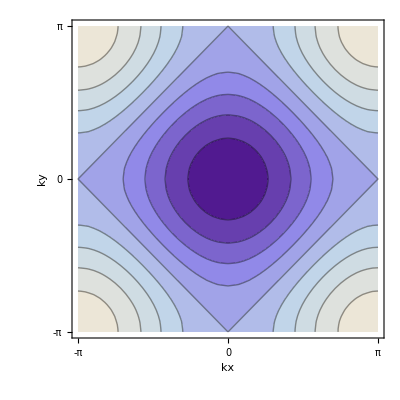

```mathematica
Image1=ContourPlot[ϵn[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```